```mathematica
Clear[k, i, p, r]
p={{0.1},{0.1},{0.1},{0.1}};
r={1.9, 2.4, 2.55, 2.7};
b=1
For[k=1, k≤ 60, k++, Do[AppendTo[p[[i]], p[[i, k]]+r*p[[i,k]]*(b-p[[i, k]])], {i, 4}]]
ListPlot[p,  PlotLegends->{"r=1.9", "r=2.4", "r=2.55", "r=2.7"}]
```

1

-Graphics-

```mathematica
Clear[k, i, p, r]

p={{0.2},{0.2},{0.2},{0.2}};
r={1.9, 2.4, 2.55, 2.7};
For[k
=1, k≤ 60, k++, Do[AppendTo[p[[i]], p[[i, k]](1-p[[i,k]])(1+r[[i]])], {i, 4}]]

ListPlot[p, PlotLegends->{"r=1.9", "r=2.4", "r=2.55", "r=2.7"}]
```

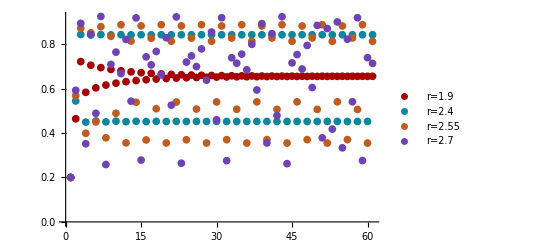

-Graphics-

1

1

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y2→InterpolatingFunction[…],x3→InterpolatingFunction[…],y3→InterpolatingFunction[…]}}

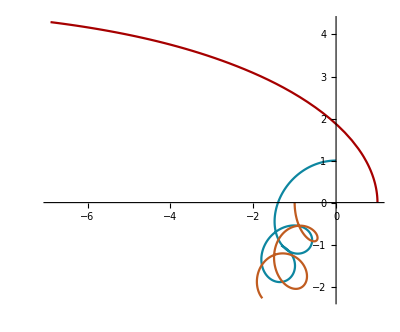

```mathematica
Clear[r,G,m,y1,y2,y3,s]
G=1
m=1
r[x1_,y1_,x2_,y2_]:=√((x1-x2)^2+(y1-y2)^2)
s=NDSolve[{x1''[t]==(-G m*(x1[t]-x2[t]))/(r[x1[t],y1[t],x2[t],y2[t]])^3-(G m*(x1[t]-x3[t]))/(r[x1[t],y1[t],x3[t],y3[t]])^3,y1''[t]==(G* m*(y2[t]-y1[t]))/(r[x1[t],y1[t],x2[t],y2[t]])^3-(G *m*(y1[t]-y3[t]))/(r[x1[t],y1[t],x3[t],y3[t]])^3,x2''[t]==(G *m*(x1[t]-x2[t]))/(r[x1[t],y1[t],x2[t],y2[t]])^3-(G *m*(x2[t]-x3[t]))/(r[x2[t],y2[t],x3[t],y3[t]])^3,y2''[t]==(-G *m*(y2[t]-y1[t]))/(r[x1[t],y1[t],x2[t],y2[t]])^3-(G *m*(y2[t]-y3[t]))/(r[x2[t],y2[t],x3[t],y3[t]])^3,x3''[t]==(G *m*(x1[t]-x3[t]))/(r[x1[t],y1[t],x3[t],y3[t]])^3+(G *m*(x2[t]-x3[t]))/(r[x2[t],y2[t],x3[t],y3[t]])^3,y3''[t]==(G *m*(y1[t]-y3[t]))/(r[x1[t],y1[t],x3[t],y3[t]])^3+(G *m*(y2[t]-y3[t]))/(r[x2[t],y2[t],x3[t],y3[t]])^3,x1[0]==1,y1[0]==0,x2[0]==0,y2[0]==1,x3[0]==-1,y3[0]==0,x1'[0]==0,y1'[0]==1,x2'[0]==-1,y2'[0]==0,x3'[0]==0,y3'[0]==-1},{x1,y1,x2,y2,x3,y3},{t,0,10}]
ParametricPlot[{{Evaluate[{x1[t],y1[t]}/.s]},{Evaluate[{x2[t],y2[t]}/.s]},{Evaluate[{x3[t],y3[t]}/.s]}},{t,0,10}]
```